```mathematica
(*MATH 484-Graphical Dual Method*)(*LP1:min z=12x1-6x2+1*)(*LP2:max z=12x1-6x2+1 with the same feasible set*)
z[x1_,x2_]:=12 x1-6 x2+1
```

```mathematica
(*LP1-STEPS 1a THROUGH 1d*)
(*LP1 Step 1a:Adjust constraints to form g>=b*)(*g1=3x1+7x2>=42 (unchanged)*)(*g2=-4x1-8x2>=-128 (flipped:4x1+8x2<=128)*)(*g3=-3x1+3x2>=-12 (flipped:3x1-3x2<=12)*)(*g4=5x1-2x2>=-10 (unchanged)*)(*Slack:si=gi(x)-bi>=0;si=0 on boundary i*)
g1[x1_,x2_]:=3 x1+7 x2;b1=42;
g2[x1_,x2_]:=-4 x1-8 x2;b2=-128;
g3[x1_,x2_]:=-3 x1+3 x2;b3=-12;
g4[x1_,x2_]:=5 x1-2 x2;b4=-10;
g1[x1_]=x2/.Solve[g1[x1,x2]==b1][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3][[1,1]];
g4[x1_]=x2/.Solve[g4[x1,x2]==b4][[1,1]];
```

```mathematica
(*LP1 Step 1b:Graph constraint boundaries and feasible set*)(*Each boundary is labeled by the slack variable that is zero*)
Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-50,50},PlotHighlighting->None,AspectRatio->Automatic,PlotRange->{-50,50},PlotLegends->Automatic]
```

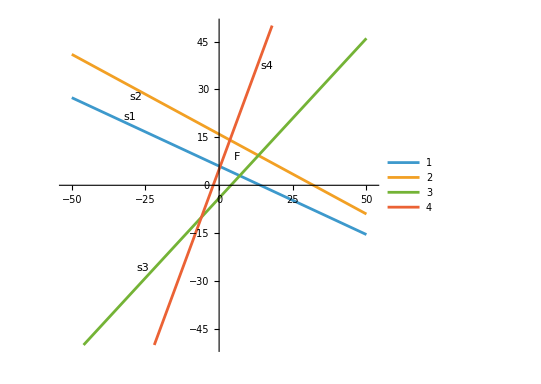

```mathematica
(*LP1 Step 1c:At each extreme point solve del-z=yi*del-gi*)
delZ={12,-6};
delG1={3,7};
delG2={-4,-8};
delG3={-3,3};
delG4={5,-2};

(*V1:s1=0,s4=0, solve y1*delG1+y4*delG4=delZ*)
lp1SolV1=Solve[y1*delG1+y4*delG4==delZ,{y1,y4}]
Print["V1 (s1=s4=0): y1,y4 = ",lp1SolV1]

(*V2:s2=0,s4=0-- solve y2*delG2+y4*delG4=delZ*)
lp1SolV2=Solve[y2*delG2+y4*delG4==delZ,{y2,y4}]
Print["V2 (s2=s4=0): y2,y4 = ",lp1SolV2]

(*V3:s2=0,s3=0-- solve y2*delG2+y3*delG3=delZ*)
lp1SolV3=Solve[y2*delG2+y3*delG3==delZ,{y2,y3}]
Print["V3 (s2=s3=0): y2,y3 = ",lp1SolV3]

(*V4:s1=0,s3=0-- solve y1*delG1+y3*delG3=delZ*)
lp1SolV4=Solve[y1*delG1+y3*delG3==delZ,{y1,y3}]
Print["V4 (s1=s3=0): y1,y3 = ",lp1SolV4]
```

{{y1→-6/41,y4→102/41}}

V1 (s1=s4=0): y1,y4 = {{y1→-6/41,y4→102/41}}

{{y2→1/8,y4→5/2}}

V2 (s2=s4=0): y2,y4 = {{y2→1/8,y4→5/2}}

{{y2→-1/2,y3→-10/3}}

V3 (s2=s3=0): y2,y3 = {{y2→-1/2,y3→-10/3}}

{{y1→3/5,y3→-17/5}}

V4 (s1=s3=0): y1,y3 = {{y1→3/5,y3→-17/5}}

```mathematica
(*LP1 Step 1d:argmin is the vertex where yi,yj are >=0*)(*V2 is y2=1/8,y4=5/2. both non-negative=>x* =V2*)(*Remaining dual variables y1=0,y3=0*)
lp1xStar={11/3,85/6};
lp1yStar={0,1/8,0,5/2};
lp1zStar=12 11/3-6 85/6+1;

Print["LP1 Step 1d: Optimal solution"]
Print["x* = ",lp1xStar," = ",N[lp1xStar]]
Print["y* = ",lp1yStar]
Print["z* = z(x*) = ",lp1zStar]
```

LP1 Step 1d: Optimal solution

x* = {11/3,85/6} = {3.66667,14.1667}

y* = {0,1/8,0,5/2}

z* = z(x*) = -40

```mathematica
(*LP2-STEPS 1a THROUGH 1d*)
(*LP2 Step 1a:Adjust constraints to form g<=b*)(*h1=-3x1-7x2<=-42 (C1 flipped:3x1+7x2>=42)*)(*h2=4x1+8x2<=128 (unchanged)*)(*h3=3x1-3x2<=12 (unchanged)*)(*h4=-5x1+2x2<=10 (C4 flipped:5x1-2x2>=-10)*)(*Slack:si=bi-hi(x)>=0;si=0 on boundary i*)
h1[x1_,x2_]:=-3 x1-7 x2;d1=-42;
h2[x1_,x2_]:=4 x1+8 x2;d2=128;
h3[x1_,x2_]:=3 x1-3 x2;d3=12;
h4[x1_,x2_]:=-5 x1+2 x2;d4=10;
h1[x1_]=x2/.Solve[h1[x1,x2]==d1][[1,1]];
h2[x1_]=x2/.Solve[h2[x1,x2]==d2][[1,1]];
h3[x1_]=x2/.Solve[h3[x1,x2]==d3][[1,1]];
h4[x1_]=x2/.Solve[h4[x1,x2]==d4][[1,1]];
```

```mathematica
(*LP2 Step 1b:Same feasible set*)
(*Boundaries and labels are identical*)
Plot[{h1[x],h2[x],h3[x],h4[x]},{x,-50,50},PlotHighlighting->None,AspectRatio->Automatic,PlotRange->{-50,50},PlotLegends->Automatic]
```

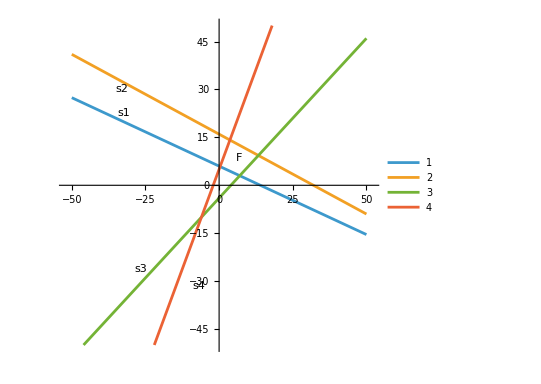

```mathematica
(*LP2 Step 1c:At each extreme point solve del-z=yi*del-hi*)(*+yj*del-hj for real yi,yj*)(*del-h1=(-3,-7),del-h2=(4,8),del-h3=(3,-3),del-h4=(-5,2)*)
delZ={12,-6};
delH1={-3,-7};
delH2={4,8};
delH3={3,-3};
delH4={-5,2};
Print["LP2 Step 1c: Dual system at each extreme point"]

(*V1:s1=0,s4=0*)
lp2SolV1=Solve[y1*delH1+y4*delH4==delZ,{y1,y4}]
Print["V1 (s1=s4=0): y1,y4 = ",lp2SolV1]

(*V2:s2=0,s4=0*)
lp2SolV2=Solve[y2*delH2+y4*delH4==delZ,{y2,y4}]
Print["V2 (s2=s4=0): y2,y4 = ",lp2SolV2]

(*V3:s2=0,s3=0*)
lp2SolV3=Solve[y2*delH2+y3*delH3==delZ,{y2,y3}]
Print["V3 (s2=s3=0): y2,y3 = ",lp2SolV3]

(*V4:s1=0,s3=0*)
lp2SolV4=Solve[y1*delH1+y3*delH3==delZ,{y1,y3}]
Print["V4 (s1=s3=0): y1,y3 = ",lp2SolV4]
```

LP2 Step 1c: Dual system at each extreme point

{{y1→6/41,y4→-102/41}}

V1 (s1=s4=0): y1,y4 = {{y1→6/41,y4→-102/41}}

{{y2→-1/8,y4→-5/2}}

V2 (s2=s4=0): y2,y4 = {{y2→-1/8,y4→-5/2}}

{{y2→1/2,y3→10/3}}

V3 (s2=s3=0): y2,y3 = {{y2→1/2,y3→10/3}}

{{y1→-3/5,y3→17/5}}

V4 (s1=s3=0): y1,y3 = {{y1→-3/5,y3→17/5}}

```mathematica
(*LP2 Step 1d:argmax is the vertex where yi,yj are both>=0*)(*V3 gives y2=1/2,y3=10/3 both non-negative=>x* =V3*)
lp2xStar={40/3,28/3};
lp2yStar={0,1/2,10/3,0};
lp2zStar=12*40/3-6*28/3 +1;

Print["=== LP2 Step 1d: Optimal solution ==="]
Print["x* = ",lp2xStar," = ",N[lp2xStar]]
Print["y* = ",lp2yStar]
Print["z* = z(x*) = ",lp2zStar]
```

=== LP2 Step 1d: Optimal solution ===

x* = {40/3,28/3} = {13.3333,9.33333}

y* = {0,1/2,10/3,0}

z* = z(x*) = 105

```mathematica
(*PROBLEM 2-STATE AND VERIFY THE DUAL LPs*)
(*LP1 Dual*)
(*Primal:min z=c.x+1 s.t.Gx>=b,x>=0*)
(*where c=(12,-6),G has rows (delG1..delG4),b=(b1..b4)*)
(*Dual LP:max w=b.y*)(*s.t.G^T y=c,y>=0*)
(*Explicitly:*)
(*max w=42y1-128y2-12y3-10y4*)
(*s.t.3y1-4y2-3y3+5y4=12*)
(*7y1-8y2+3y3-2y4=-6*)
(*y1,y2,y3,y4>=0*)
(*Solution y* =(y1,y2,y3,y4) found in Step 1c at x**)
(*w* =b.y*should equal z*-1 (constant offset in primal)*)
lp1DualObj={b1,b2,b3,b4}.lp1yStar;
lp1DualConstraintCheck={{3,-4,-3,5}.lp1yStar==12,{7,-8,3,-2}.lp1yStar==-6};

Print["=== Problem 2: LP1 Dual ==="]
Print["Dual LP: max w = 42y1 - 128y2 - 12y3 - 10y4"]
Print["s.t.  3y1 -  4y2 - 3y3 + 5y4 = 12"]
Print["      7y1 -  8y2 + 3y3 - 2y4 = -6"]
Print["      y1, y2, y3, y4 >= 0"]
Print["y* = ",lp1yStar]
Print["w* = b.y* = ",lp1DualObj]
Print["z* - 1 = ",lp1zStar-1]
Print["Dual constraint 1 satisfied: ",lp1DualConstraintCheck[[1]]]
Print["Dual constraint 2 satisfied: ",lp1DualConstraintCheck[[2]]]
Print["Verify Z*: ",lp1DualObj==lp1zStar-1]
```

=== Problem 2: LP1 Dual ===

Dual LP: max w = 42y1 - 128y2 - 12y3 - 10y4

s.t.  3y1 -  4y2 - 3y3 + 5y4 = 12

7y1 -  8y2 + 3y3 - 2y4 = -6

y1, y2, y3, y4 >= 0

y* = {0,1/8,0,5/2}

w* = b.y* = -41

z* - 1 = -41

Dual constraint 1 satisfied: True

Dual constraint 2 satisfied: True

Verify Z*: True

```mathematica
(*LP2 Dual*)
(*Primal:max z=c.x+1 s.t.Hx<=d,x>=0*)(*where c=(12,-6),H has rows (delH1..delH4),d=(d1..d4)*)
(*Dual LP:min w=d.y*)(*s.t.H^T y=c,y>=0*)
(*Explicitly:*)
(*min w=-42y1+128y2+12y3+10y4*)
(*s.t.-3y1+4y2+3y3-5y4=12*)
(*-7y1+8y2-3y3+2y4=-6*)
(*y1,y2,y3,y4>=0*)
(*Solution y* =(y1,y2,y3,y4) found in Step 1c at x**)
(*w* =d.y*should equal z*-1 (constant offset in primal)*)
lp2DualObj={d1,d2,d3,d4}.lp2yStar;
lp2DualConstraintCheck={{-3,4,3,-5}.lp2yStar==12,{-7,8,-3,2}.lp2yStar==-6};

Print["=== Problem 2: LP2 Dual ==="]
Print["Dual LP: min w = -42y1 + 128y2 + 12y3 + 10y4"]
Print["s.t. -3y1 + 4y2 + 3y3 - 5y4 = 12"]
Print["     -7y1 + 8y2 - 3y3 + 2y4 = -6"]
Print["      y1, y2, y3, y4 >= 0"]
Print["y* = ",lp2yStar]
Print["w* = d.y* = ",lp2DualObj]
Print["z* - 1 = ",lp2zStar-1]
Print["Dual constraint 1 satisfied: ",lp2DualConstraintCheck[[1]]]
Print["Dual constraint 2 satisfied: ",lp2DualConstraintCheck[[2]]]
Print["Verify Z*",lp2DualObj==lp2zStar-1]
```

=== Problem 2: LP2 Dual ===

Dual LP: min w = -42y1 + 128y2 + 12y3 + 10y4

s.t. -3y1 + 4y2 + 3y3 - 5y4 = 12

-7y1 + 8y2 - 3y3 + 2y4 = -6

y1, y2, y3, y4 >= 0

y* = {0,1/2,10/3,0}

w* = d.y* = 104

z* - 1 = 104

Dual constraint 1 satisfied: True

Dual constraint 2 satisfied: True

Verify Z*True